```mathematica
data=Import"D:\\code\\plecs\\github\\plecs\\exercise\\PLECS视频教程10相关文件\\data.csv"];data=data⟦2;;⟧;
```

```mathematica
amp=Interpolation[data⟦;;,{1,2}⟧]
```

InterpolatingFunction[…]

```mathematica
phase=Interpolation[data⟦;;,{1,3}⟧]
```

InterpolatingFunction[…]

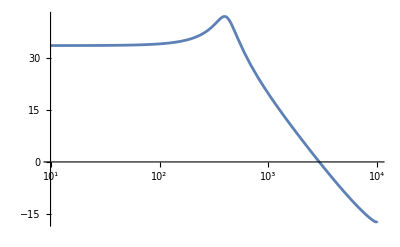

```mathematica
Plot[amp[f],{f,10,10*^3},ScalingFunctions->{"Log10",None}]
```

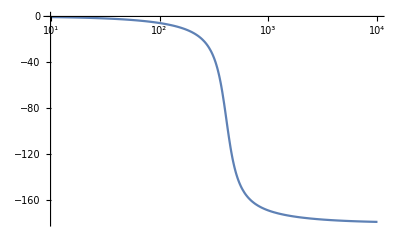

```mathematica
Plot[phase[f],{f,10,10*^3},ScalingFunctions->{"Log10",None}]
```

```mathematica
Manipulate[{LogLinearPlot[{20Log[10,Abs[kp (t+s)/s]],20Log[10,Abs[kp (t+s)/s]]+amp[f],amp[f]}//.s->ⅈ 2π f//ComplexExpand//Evaluate,{f,10,10*^3},PlotRange->{-50,80},PlotLegends->{PI控制器,环路增益,被控对象}],LogLinearPlot[{Arg[kp (t+s)/s] 180/π,Arg[kp (t+s)/s] 180/π+phase[f],phase[f],-180}//.s->ⅈ 2π f//ComplexExpand//Evaluate,{f,10,10*^3},PlotRange->{-200,50},PlotLegends->{PI控制器,环路增益,被控对象}]},{kp,1*^-3,1},{t,1*^2,1*^4}]
```